```mathematica
PolynomialMod[Sum[2^n*x^n,{n,0,15}],x^16+1,Modulus->3329]
```

1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10+2048 x^11+767 x^12+1534 x^13+3068 x^14+2807 x^15

```mathematica
PolynomialMod[Sum[(n+1)*x^n,{n,0,15}],x^16+1,Modulus->3329]
```

1+2 x+3 x^2+4 x^3+5 x^4+6 x^5+7 x^6+8 x^7+9 x^8+10 x^9+11 x^10+12 x^11+13 x^12+14 x^13+15 x^14+16 x^15

```mathematica
PolynomialMod[Sum[2^n*x^n,{n,0,15}]*Sum[(n+1)*x^n,{n,0,15}],x^16+1,Modulus->3329]
```

3169+923 x+2046 x^2+3249 x^3+1283 x^4+2966 x^5+1960 x^6+2234 x^7+1739 x^8+3035 x^9+1255 x^10+3310 x^11+3048 x^12+1481 x^13+633 x^14+1223 x^15

```mathematica
PolynomialMod[Sum[2^n*x^n,{n,0,15}]+Sum[(n+1)*x^n,{n,0,15}],x^16+1,Modulus->3329]
```

2+4 x+7 x^2+12 x^3+21 x^4+38 x^5+71 x^6+136 x^7+265 x^8+522 x^9+1035 x^10+2060 x^11+780 x^12+1548 x^13+3083 x^14+2823 x^15

```mathematica
PolynomialMod[Sum[x^n,{n,0,15}]*Sum[x^n,{n,0,15}],x^16+1,Modulus->3329]
```

3315+3317 x+3319 x^2+3321 x^3+3323 x^4+3325 x^5+3327 x^6+2 x^8+4 x^9+6 x^10+8 x^11+10 x^12+12 x^13+14 x^14+16 x^15

```mathematica
Table[Mod[-14 + 2n,3329],{n,0,15}]
```

{3315,3317,3319,3321,3323,3325,3327,0,2,4,6,8,10,12,14,16}

```mathematica
DiscretePlot[{Mod[x,3329], Mod[x,2^16]},{x,-2^16,2^16}]
```

-Graphics-

```mathematica
DiscretePlot[{Mod[x,3329], Mod[x,2^16],Mod[Mod[x,2^16],3329]},{x,-2^16,2^16}]
```

-Graphics-

```mathematica
Mod[-2^16,3329]
```

1044

```mathematica
Manipulate[{"2^16: " Text[Mod[x,2^16]],"3329: "Text[Mod[x,3329]],"Test: "Text[Mod[Mod[x,2^16]+1044,3329]-Mod[x,3329]]},{x,-5000,5000,1}]
```

```mathematica
2^64
```

18446744073709551616

```mathematica
BitShiftLeft[1,64]
```

18446744073709551616

```mathematica
3329-Mod[2^16,3329]
```

1044

```mathematica
Manipulate[{"2^16: " Text[Mod[x,2^16]],"3329: "Text[Mod[x,3329]],"Test: "Text[Mod[Mod[Mod[x,2^16]+1044,2^16],3329]-Mod[x,3329]]},{x,-5000,5000,1}]
```

```mathematica
Manipulate[{"2^16: " Text[Mod[x,2^8]],"3329: "Text[Mod[x,3329]],"Test: "Text[Mod[Mod[x,2^8]+(3329 - Mod[2^8,3329]),3329]-Mod[x,3329]]},{x,-5000,5000,1}]
```

```mathematica
Manipulate[{"2^16: " Text[Mod[x,2^16]],"3329: "Text[Mod[x,3329]],"Test: "Text[Mod[Mod[Mod[x,2^16]+1044 -3329,2^16],3329]-Mod[x,3329]]},{x,-5000,5000,1}]
```

```mathematica
Manipulate[{"2^64: " Text[Mod[x,2^64]],"3329: "Text[Mod[x,3329]],"Test: "Text[Mod[Mod[Mod[x,2^64]+1044 -3329,2^64],3329]-Mod[x,3329]]},{x,-5000,5000,1}]
```

```mathematica
Manipulate[{"2^64: " Text[Mod[x,2^64]],"3329: "Text[Mod[x,3329]],"Test: "Text[Mod[Mod[x,2^64]+(3329 - Mod[2^64,3329])-3329^3,3329]-Mod[x,3329]]},{x,-2^32,2^32,1}]
```

```mathematica
2^16
```

65536

```mathematica
Mod[Mod[x,2^64]+(3329 - Mod[2^64,3329])-3329,3329]-Mod[x,3329]==0
```

-Mod[x,3329]+Mod[-2988+Mod[x,18446744073709551616],3329]==0

```mathematica
Solve[-Mod[x,3329]+Mod[-2988+Mod[x,18446744073709551616],3329]==0,{x},Integers]
```

Solve::mpwc: Solve was unable to convert Floor[-2988/3329+(x-18446744073709551616 Floor[x/18446744073709551616])/3329] to Piecewise because the required number 5541226816974934 of piecewise cases sought exceeds the internal limit $MaxPiecewiseCases = 100.

Solve[-Mod[x,3329]+Mod[-2988+Mod[x,18446744073709551616],3329]==0,{x},ℤ]

```mathematica
Solve[-Mod[x,3329]+Mod[-36892779948+Mod[x,18446744073709551616],3329]==0,{x},NegativeIntegers]
```

Solve::mpwc: Solve was unable to convert Floor[-36892779948/3329+(x-18446744073709551616 Floor[x/18446744073709551616])/3329] to Piecewise because the required number 5541226816974934 of piecewise cases sought exceeds the internal limit $MaxPiecewiseCases = 100.

Solve[-Mod[x,3329]+Mod[-36892779948+Mod[x,18446744073709551616],3329]==0,{x},]

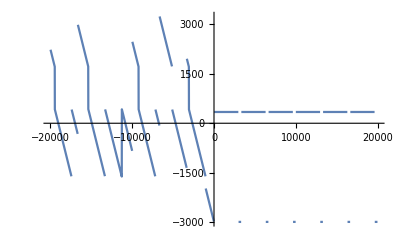

```mathematica
Plot[-Mod[x,3329]+Mod[-36892779948+Mod[x,18446744073709551616],3329],{x,-19974.,19974.}]
```

```mathematica
PolynomialMod[Sum[3328*x^n,{n,1,255}]*Sum[3328*x^n,{n,1,255}],x^256+1]
```

-2824273920-2813198336 x-2791047168 x^2-2768896000 x^3-2746744832 x^4-2724593664 x^5-2702442496 x^6-2680291328 x^7-2658140160 x^8-2635988992 x^9-2613837824 x^10-2591686656 x^11-2569535488 x^12-2547384320 x^13-2525233152 x^14-2503081984 x^15-2480930816 x^16-2458779648 x^17-2436628480 x^18-2414477312 x^19-2392326144 x^20-2370174976 x^21-2348023808 x^22-2325872640 x^23-2303721472 x^24-2281570304 x^25-2259419136 x^26-2237267968 x^27-2215116800 x^28-2192965632 x^29-2170814464 x^30-2148663296 x^31-2126512128 x^32-2104360960 x^33-2082209792 x^34-2060058624 x^35-2037907456 x^36-2015756288 x^37-1993605120 x^38-1971453952 x^39-1949302784 x^40-1927151616 x^41-1905000448 x^42-1882849280 x^43-1860698112 x^44-1838546944 x^45-1816395776 x^46-1794244608 x^47-1772093440 x^48-1749942272 x^49-1727791104 x^50-1705639936 x^51-1683488768 x^52-1661337600 x^53-1639186432 x^54-1617035264 x^55-1594884096 x^56-1572732928 x^57-1550581760 x^58-1528430592 x^59-1506279424 x^60-1484128256 x^61-1461977088 x^62-1439825920 x^63-1417674752 x^64-1395523584 x^65-1373372416 x^66-1351221248 x^67-1329070080 x^68-1306918912 x^69-1284767744 x^70-1262616576 x^71-1240465408 x^72-1218314240 x^73-1196163072 x^74-1174011904 x^75-1151860736 x^76-1129709568 x^77-1107558400 x^78-1085407232 x^79-1063256064 x^80-1041104896 x^81-1018953728 x^82-996802560 x^83-974651392 x^84-952500224 x^85-930349056 x^86-908197888 x^87-886046720 x^88-863895552 x^89-841744384 x^90-819593216 x^91-797442048 x^92-775290880 x^93-753139712 x^94-730988544 x^95-708837376 x^96-686686208 x^97-664535040 x^98-642383872 x^99-620232704 x^100-598081536 x^101-575930368 x^102-553779200 x^103-531628032 x^104-509476864 x^105-487325696 x^106-465174528 x^107-443023360 x^108-420872192 x^109-398721024 x^110-376569856 x^111-354418688 x^112-332267520 x^113-310116352 x^114-287965184 x^115-265814016 x^116-243662848 x^117-221511680 x^118-199360512 x^119-177209344 x^120-155058176 x^121-132907008 x^122-110755840 x^123-88604672 x^124-66453504 x^125-44302336 x^126-22151168 x^127+22151168 x^129+44302336 x^130+66453504 x^131+88604672 x^132+110755840 x^133+132907008 x^134+155058176 x^135+177209344 x^136+199360512 x^137+221511680 x^138+243662848 x^139+265814016 x^140+287965184 x^141+310116352 x^142+332267520 x^143+354418688 x^144+376569856 x^145+398721024 x^146+420872192 x^147+443023360 x^148+465174528 x^149+487325696 x^150+509476864 x^151+531628032 x^152+553779200 x^153+575930368 x^154+598081536 x^155+620232704 x^156+642383872 x^157+664535040 x^158+686686208 x^159+708837376 x^160+730988544 x^161+753139712 x^162+775290880 x^163+797442048 x^164+819593216 x^165+841744384 x^166+863895552 x^167+886046720 x^168+908197888 x^169+930349056 x^170+952500224 x^171+974651392 x^172+996802560 x^173+1018953728 x^174+1041104896 x^175+1063256064 x^176+1085407232 x^177+1107558400 x^178+1129709568 x^179+1151860736 x^180+1174011904 x^181+1196163072 x^182+1218314240 x^183+1240465408 x^184+1262616576 x^185+1284767744 x^186+1306918912 x^187+1329070080 x^188+1351221248 x^189+1373372416 x^190+1395523584 x^191+1417674752 x^192+1439825920 x^193+1461977088 x^194+1484128256 x^195+1506279424 x^196+1528430592 x^197+1550581760 x^198+1572732928 x^199+1594884096 x^200+1617035264 x^201+1639186432 x^202+1661337600 x^203+1683488768 x^204+1705639936 x^205+1727791104 x^206+1749942272 x^207+1772093440 x^208+1794244608 x^209+1816395776 x^210+1838546944 x^211+1860698112 x^212+1882849280 x^213+1905000448 x^214+1927151616 x^215+1949302784 x^216+1971453952 x^217+1993605120 x^218+2015756288 x^219+2037907456 x^220+2060058624 x^221+2082209792 x^222+2104360960 x^223+2126512128 x^224+2148663296 x^225+2170814464 x^226+2192965632 x^227+2215116800 x^228+2237267968 x^229+2259419136 x^230+2281570304 x^231+2303721472 x^232+2325872640 x^233+2348023808 x^234+2370174976 x^235+2392326144 x^236+2414477312 x^237+2436628480 x^238+2458779648 x^239+2480930816 x^240+2503081984 x^241+2525233152 x^242+2547384320 x^243+2569535488 x^244+2591686656 x^245+2613837824 x^246+2635988992 x^247+2658140160 x^248+2680291328 x^249+2702442496 x^250+2724593664 x^251+2746744832 x^252+2768896000 x^253+2791047168 x^254+2813198336 x^255

```mathematica
2^64
```

18446744073709551616

```mathematica
(2^64+3329/2)/3329
```

```mathematica
36893488147419106561/6658*2824273920
```

52098658196292448984966594560/3329

```mathematica
N[52098658196292448984966594560/3329]
```

```mathematica
1.564994238398692*^25-2^64
```

1.56499×10^25

```mathematica
2^24
```

16777216

```mathematica
Manipulate[{Mod[Floor[x],3329], ((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,24]+Floor[3329/2])/3329],24]*3329)-3329) + If[((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,24]+Floor[3329/2])/3329],24]*3329)-3329)<0 ,3329,0]},{x,0,10000000,1}]
```

```mathematica
2^11
```

2048

```mathematica
2
```

```mathematica
Manipulate[{Mod[Floor[x],3329], ((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329) + If[((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329)<0 ,3329,0]},{x,0,2^32,1}]
```

```mathematica
DiscretePlot[{Mod[Floor[x],3329], ((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329) + If[((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329)<0 ,3329,0]},{x,0,2^32}]
```

```mathematica
Solve[Mod[Floor[x],3329] == ((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329) + If[((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329)<0 ,3329,0],x∈PositiveIntegers]
```

Solve::ivar: x∈&&x>0 is not a valid variable.

```mathematica
Solve[Mod[Floor[x],3329]==-3329-3329 BitShiftRight[1290167 Floor[x],32]+Floor[x]+If[-3329-3329 BitShiftRight[1290167 Floor[x],32]+Floor[x]<0,3329,0],x,PositiveIntegers]
```

Solve[Mod[Floor[x],3329]==-3329-3329 BitShiftRight[1290167 Floor[x],32]+Floor[x]+If[-3329-3329 BitShiftRight[1290167 Floor[x],32]+Floor[x]<0,3329,0],x,]

```mathematica
NSolve[Mod[x,3329]!=-3329-3329 BitShiftRight[1290167 x,32]+x+If[-3329-3329 BitShiftRight[1290167x,32]+x<0,3329,0],x,]
```

NSolve[Mod[x,3329]≠-3329+x-3329 BitShiftRight[1290167 x,32]+If[-3329+x-3329 BitShiftRight[1290167 x,32]<0,3329,0],x,]

```mathematica
Solve[Mod[Floor[x],3329] == ((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329) + If[((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329)<0 ,3329,0],x,PositiveIntegers]
```

Solve[Mod[Floor[x],3329]==-3329-3329 BitShiftRight[1290167 Floor[x],32]+Floor[x]+If[-3329-3329 BitShiftRight[1290167 Floor[x],32]+Floor[x]<0,3329,0],x,]

```mathematica
Manipulate[Mod[Mod[Floor[x],3329]-((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329) + If[((Floor[x]-BitShiftRight[Floor[x]*Floor[(BitShiftLeft[1,32]+Floor[3329/2])/3329],32]*3329)-3329)<0 ,3329,0],3329],{x,0,2^32,1}]
```

```mathematica
BitShiftLeft[1,64]
```

18446744073709551616

```mathematica
BitLength[18446744073709551616]
```

65

```mathematica
18446744073709551616 + Floor[3329/2]
```

18446744073709553280

```mathematica
Floor[18446744073709553280/3329]
```

5541226816974933

```mathematica
BitLength[5541226816974933]
```

53

```mathematica
2824273920 *5541226816974933
```

15649942383986916565647360

```mathematica
BitLength[15649942383986916565647360]
```

84

```mathematica
Mod[-5000000, BitShiftLeft[1, 64]] - BitAnd[Mod[BitShiftLeft[1, 64],3329],BitShiftRight[-5000000,63]]
```

18446744073704551616

```mathematica
Mod[-5000000, BitShiftLeft[1, 64]]
```

18446744073704551616

```mathematica
BitAnd[Mod[BitShiftLeft[1, 64],3329],BitShiftRight[-5000000,63]]
```

0

```mathematica
Mod[BitShiftLeft[1, 63],3329]
```

1494

```mathematica
3329-1494
```

1835

```mathematica
BitShiftRight[-5000000,63]
```

0

```mathematica
Mod[-5000000, 3329]
```

158

```mathematica
Manipulate[{"2^64: " Text[Mod[Floor[x],2^64]],"3329: "Text[Mod[Floor[x],3329]],"Test: "Text[Mod[Mod[Floor[x],2^64]- Mod[2^64,3329],3329]-Mod[Floor[x],3329]]},{x,-2^32,2^32,1}]
```

```mathematica
Table[Mod[x,3329],{x,{10000, -10000, 5000, -5000, 2000, -2000, 1000, -1000, 500, -500, 250, -250, 125, -125, 62, -62}}]
```

{13,3316,1671,1658,2000,1329,1000,2329,500,2829,250,3079,125,3204,62,3267}

```mathematica
2^128
```

340282366920938463463374607431768211456

```mathematica
2^64
```

18446744073709551616

```mathematica
5657-3329
```

2328

```mathematica
Mod[5657,3329]
```

2328

```mathematica
Manipulate[{"2^32: " Text[Mod[Floor[x],2^32]],"3329: "Text[Mod[Floor[x],3329]],"Test: "Text[Mod[Mod[Floor[x],2^32]- Mod[2^32,3329],3329]-Mod[Floor[x],3329]]},{x,-2^16,2^16,1}]
```

```mathematica
A = {500, 4294965443, 250, 4294965693, 125, 4294965818, 62, 4294965881};
B = {1290167, 1290167, 1290167, 1290167, 1290167, 1290167, 1290167, 1290167};
```

```mathematica
A*B
```

{645083500,5541222680698981,322541750,5541223003240731,161270875,5541223164511606,79990354,5541223245792127}

```mathematica
Table[NumberForm[BaseForm[x,2],64, NumberPadding->{"0",""}], {x,%5}]
```

{00000000000000000000000000000000000100110011100110011000101101100_2,00000000000010011101011111011011001110001100000010010000001100101_2,00000000000000000000000000000000000010011001110011001100010110110_2,00000000000010011101011111011011010000100101110101011100100011011_2,00000000000000000000000000000000000001001100111001100110001011011_2,00000000000010011101011111011011010001110010101111000010101110110_2,00000000000000000000000000000000000000100110001001000111001010010_2,00000000000010011101011111011011010010011001011111100001101111111_2}

```mathematica
Table[FromDigits[#]&/@{IntegerDigits[x][[1;;32]],IntegerDigits[x][[32;;64]]},{x,%}]
```

Part::take: Cannot take positions 1 through 32 in {IntegerDigits[FromDigits[00000000000000000000000000000000000100110011100110011000101101100_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000100110011100110011000101101100_2⟦32;;64⟧]]}.

Part::take: Cannot take positions 32 through 64 in {IntegerDigits[FromDigits[00000000000000000000000000000000000100110011100110011000101101100_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000100110011100110011000101101100_2⟦32;;64⟧]]}.

PaddedForm::npad: Value for option NumberPadding -> {«2»} should be a string or a pair of strings.

FromDigits::nlst: The expression {IntegerDigits[FromDigits[100110011100110011000101101100_2⟦1;;32⟧]],IntegerDigits[FromDigits[100110011100110011000101101100_2⟦32;;64⟧]]}⟦1;;32⟧ is not a list of digits or a string of valid digits.

PaddedForm::npad: Value for option NumberPadding -> {«2»} should be a string or a pair of strings.

General::stop: Further output of PaddedForm::npad will be suppressed during this calculation.

FromDigits::nlst: The expression {IntegerDigits[FromDigits[100110011100110011000101101100_2⟦1;;32⟧]],IntegerDigits[FromDigits[100110011100110011000101101100_2⟦32;;64⟧]]}⟦32;;64⟧ is not a list of digits or a string of valid digits.

Part::take: Cannot take positions 1 through 32 in {IntegerDigits[FromDigits[00000000000010011101011111011011001110001100000010010000001100101_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000010011101011111011011001110001100000010010000001100101_2⟦32;;64⟧]]}.

General::stop: Further output of Part::take will be suppressed during this calculation.

FromDigits::nlst: The expression {IntegerDigits[FromDigits[10011101011111011011001110001100000010010000001100101_2⟦1;;32⟧]],IntegerDigits[FromDigits[10011101011111011011001110001100000010010000001100101_2⟦32;;64⟧]]}⟦1;;32⟧ is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

{{FromDigits[{IntegerDigits[FromDigits[00000000000000000000000000000000000100110011100110011000101101100_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000100110011100110011000101101100_2⟦32;;64⟧]]}⟦1;;32⟧],FromDigits[{IntegerDigits[FromDigits[00000000000000000000000000000000000100110011100110011000101101100_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000100110011100110011000101101100_2⟦32;;64⟧]]}⟦32;;64⟧]},{FromDigits[{IntegerDigits[FromDigits[00000000000010011101011111011011001110001100000010010000001100101_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000010011101011111011011001110001100000010010000001100101_2⟦32;;64⟧]]}⟦1;;32⟧],FromDigits[{IntegerDigits[FromDigits[00000000000010011101011111011011001110001100000010010000001100101_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000010011101011111011011001110001100000010010000001100101_2⟦32;;64⟧]]}⟦32;;64⟧]},{FromDigits[{IntegerDigits[FromDigits[00000000000000000000000000000000000010011001110011001100010110110_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000010011001110011001100010110110_2⟦32;;64⟧]]}⟦1;;32⟧],FromDigits[{IntegerDigits[FromDigits[00000000000000000000000000000000000010011001110011001100010110110_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000010011001110011001100010110110_2⟦32;;64⟧]]}⟦32;;64⟧]},{FromDigits[{IntegerDigits[FromDigits[00000000000010011101011111011011010000100101110101011100100011011_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000010011101011111011011010000100101110101011100100011011_2⟦32;;64⟧]]}⟦1;;32⟧],FromDigits[{IntegerDigits[FromDigits[00000000000010011101011111011011010000100101110101011100100011011_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000010011101011111011011010000100101110101011100100011011_2⟦32;;64⟧]]}⟦32;;64⟧]},{FromDigits[{IntegerDigits[FromDigits[00000000000000000000000000000000000001001100111001100110001011011_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000001001100111001100110001011011_2⟦32;;64⟧]]}⟦1;;32⟧],FromDigits[{IntegerDigits[FromDigits[00000000000000000000000000000000000001001100111001100110001011011_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000001001100111001100110001011011_2⟦32;;64⟧]]}⟦32;;64⟧]},{FromDigits[{IntegerDigits[FromDigits[00000000000010011101011111011011010001110010101111000010101110110_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000010011101011111011011010001110010101111000010101110110_2⟦32;;64⟧]]}⟦1;;32⟧],FromDigits[{IntegerDigits[FromDigits[00000000000010011101011111011011010001110010101111000010101110110_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000010011101011111011011010001110010101111000010101110110_2⟦32;;64⟧]]}⟦32;;64⟧]},{FromDigits[{IntegerDigits[FromDigits[00000000000000000000000000000000000000100110001001000111001010010_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000000100110001001000111001010010_2⟦32;;64⟧]]}⟦1;;32⟧],FromDigits[{IntegerDigits[FromDigits[00000000000000000000000000000000000000100110001001000111001010010_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000000000000000000000000000000100110001001000111001010010_2⟦32;;64⟧]]}⟦32;;64⟧]},{FromDigits[{IntegerDigits[FromDigits[00000000000010011101011111011011010010011001011111100001101111111_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000010011101011111011011010010011001011111100001101111111_2⟦32;;64⟧]]}⟦1;;32⟧],FromDigits[{IntegerDigits[FromDigits[00000000000010011101011111011011010010011001011111100001101111111_2⟦1;;32⟧]],IntegerDigits[FromDigits[00000000000010011101011111011011010010011001011111100001101111111_2⟦32;;64⟧]]}⟦32;;64⟧]}}

```mathematica
nums={645083500,5541222680698981,322541750,5541223003240731,161270875,5541223164511606,79990354,5541223245792127};

(*force into unsigned 64-bit range just in case*)
u64=Mod[nums,2^64];

(*{hi32,lo32} for each 64-bit number*)
pairsDec=({BitShiftRight[#,32],BitAnd[#,2^32-1]}&)/@u64;

(*same,but shown in hex (zero-padded)*)
pairsHex={IntegerString[BitShiftRight[#,32],16,8],IntegerString[BitAnd[#,2^32-1],16,8]}&/@u64;

(*optional:full 64-bit binary (zero-padded to 64)*)
bin64=IntegerString[#,2,64]&/@u64;
```

```mathematica
pairsDec
```

{{0,645083500},{1290166,1904287845},{0,322541750},{1290166,2226829595},{0,161270875},{1290166,2388100470},{0,79990354},{1290166,2469380991}}

```mathematica
bin64
```

{0000000000000000000000000000000000100110011100110011000101101100,0000000000010011101011111011011001110001100000010010000001100101,0000000000000000000000000000000000010011001110011001100010110110,0000000000010011101011111011011010000100101110101011100100011011,0000000000000000000000000000000000001001100111001100110001011011,0000000000010011101011111011011010001110010101111000010101110110,0000000000000000000000000000000000000100110001001000111001010010,0000000000010011101011111011011010010011001011111100001101111111}

```mathematica
bin64h={IntegerString[BitShiftRight[#,32],2,32],IntegerString[BitAnd[#,2^32-1],2,32]}&/@u64;
```

```mathematica
bin64h
```

{{00000000000000000000000000000000,00100110011100110011000101101100},{00000000000100111010111110110110,01110001100000010010000001100101},{00000000000000000000000000000000,00010011001110011001100010110110},{00000000000100111010111110110110,10000100101110101011100100011011},{00000000000000000000000000000000,00001001100111001100110001011011},{00000000000100111010111110110110,10001110010101111000010101110110},{00000000000000000000000000000000,00000100110001001000111001010010},{00000000000100111010111110110110,10010011001011111100001101111111}}